```mathematica
Clear["Global`*"]
(*creating mountain range*)
m1[x_,y_]=ⅇ^-(1*√((x-1)^2+(y-1.1)^2))^2;
m2[x_,y_]=ⅇ^-(3*√((x-3)^2+(y-2)^2))^2;
m3[x_,y_]=ⅇ^-(1*√((x-4)^2+(y-1)^2))^2;
m4[x_,y_]=ⅇ^-(2*√((x-4)^2+(y-3.5)^2))^2;
m5[x_,y_]=ⅇ^-(3*√((x-3)^2+(y-3.5)^2))^2;
m6[x_,y_]=ⅇ^-(2*√((x-2)^2+(y-3)^2))^2;
m7[x_,y_]=ⅇ^-(2*√((x-4)^2+(y-2)^2))^2;
M[x_,y_]=(1.5*m1[x,y]+0.5*m2[x,y]+0.5*m3[x,y]+1*m4[x,y]+0.75*m5[x,y]+1*m6[x,y]+0.5*m7[x,y])+7;
Mx[x_,y_] = D[M[x,y],x];
My[x_,y_] = D[M[x,y],y];
Gradm[x_,y_]=Grad[My[x,y], {x,y}];
```

{0.7,2.}

-0.757415

{1.846,{t→0.948812}}

{-0.146833,{t→2.8926}}

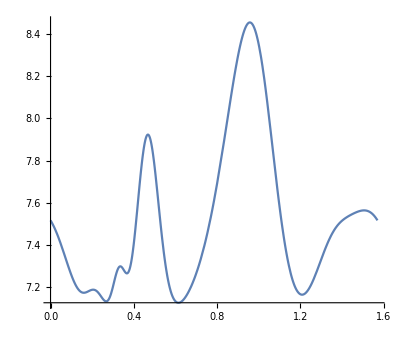

lagrange

-1+0.308642 (-2.5+x)^2+0.694444 (-2+y)^2

0.617284 (-2.5+x)

1.38889 (-2+y)

{x→1.11092,y→1.23683,λ→0.375482}

-1.11022×10^-16

8.45429

max2

{8.45429,{t→0.957716}}

min

{7.12697,{t→0.614674}}

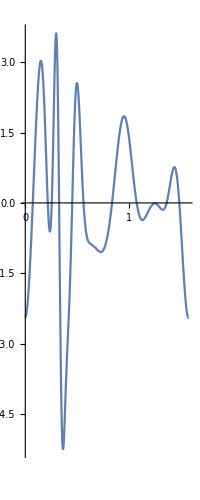

{1.846,{t→0.948812}}

-Graphics3D-

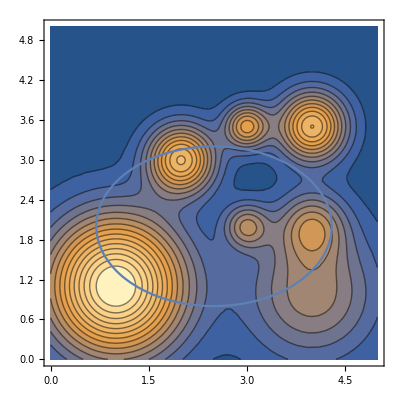

```mathematica
(*x and y define the 2d path we take*)
x[t_]= 2.5 + 1.8*Cos[(4*t)];
y[t_]= 2 + 1.2*Sin[(4*t)];
x1[t_] = D[x[t], t];
y1[t_] = D[y[t],t];
r[t_]= {x[t],y[t]};
v[t_] =D[r[t], t];
u[t_] = Normalize[v[t]];
G[t_] = Gradm[x[t], y[t]];
(*the directional derv is the gradient dotted with the directional unit tangent *)
d[t_]= Dot[G[t],u[t] ];
(*honeybadger location*)
badger = {x[π/4],y[π/4]}
(*honey badger slope*)
slope = d[π/4]
(*greatest and least rate of change/slope*)
FindMaximum[d[t], {t, 0.4 }]
FindMinimum[d[t], {t, 0.5}]
(*highest point*)
ParametricPlot[{t, M[x[t],y[t]]}, {t,0,π/2}]
lagrange
(*reparametrized the route function*)
R[x_,y_]=((x-2.5)/1.8)^2+((y-2)/(-1.2))^2-1
Rx[x_,y_]= D[R[x,y], {x}]
Ry[x_,y_]= D[R[x,y], {y}]
FindRoot[{Mx[x,y] == λ*Rx[x,y],My[x,y] == λ*Ry[x,y],R[x,y]== 0},{x,0.9}, {y,1}, {λ, 0}]
(*height at max*)
M[1.1109245153622094,1.2368284602388133]
max2
FindMaximum[M[x[t],y[t]], {t, 1}]
min
FindMinimum[M[x[t],y[t]], {t, 0.6}]

ParametricPlot[{t, d[t]}, {t,0,π/2}]
FindMaximum[d[t], {t, 0.4 }] 
route = ParametricPlot[{x[t],y[t]},{t, 0, π/2}];
route3d = ParametricPlot3D[{x[t],y[t], M[x[t],y[t]]},{t, 0, π/2}];
mountains = Plot3D[M[x,y],{x,0,5},{y,0,5}];
test  = ContourPlot[M[x,y], {x,0,5},{y,0,5}, Contours->15];
Show[mountains, route3d, PlotRange-> All]
Show[test, route, PlotRange -> All]
```